```mathematica
Needs["BezierCurveApproximation`"]
```

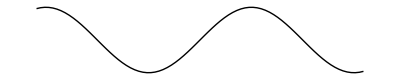

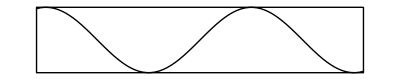

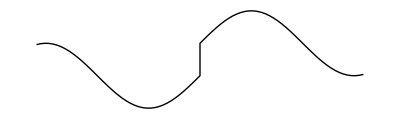

```mathematica
PlotBezier[Sin[t],{t,{-5,-4,-3,-2,-1,0,1,2,3,4,5}}]
PlotBezier[Sin[t],{t,{-5,-4,-3,-2,-1,0,1,2,3,4,5}},BoundingBox->{{5,1},{-5,-1}}]
PlotBezier[Sin[t]+UnitStep[t],{t,{-5,-4,-3,-2,-1,0,1,2,3,4,5}}]
```

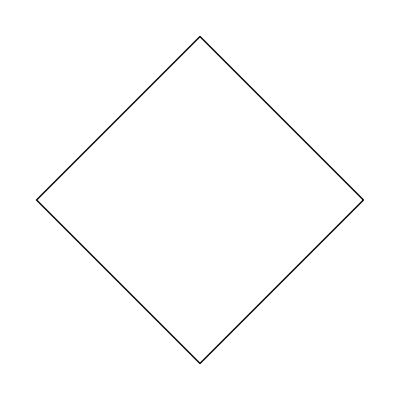
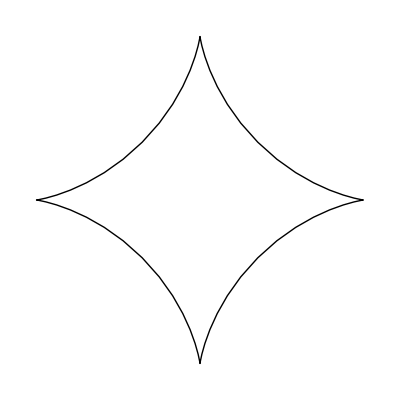
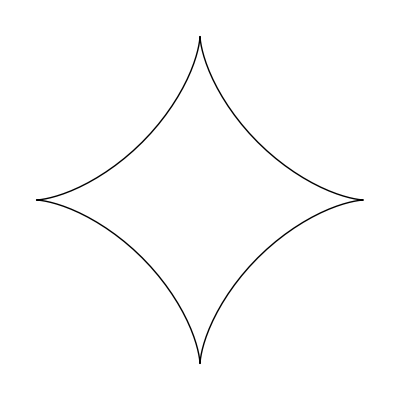

```mathematica
{ParametricPlotBezier[{Cos[t]^3,Sin[t]^3},{t,π/2 Table[i,{i,0,4}]}],
ParametricPlotBezier[{Cos[t]^3,Sin[t]^3},{t,π/4 Table[i,{i,0,8}]}],
ParametricPlotBezier[{Cos[t]^3,Sin[t]^3},{t,π/8 Table[i,{i,0,16}]}]}
```

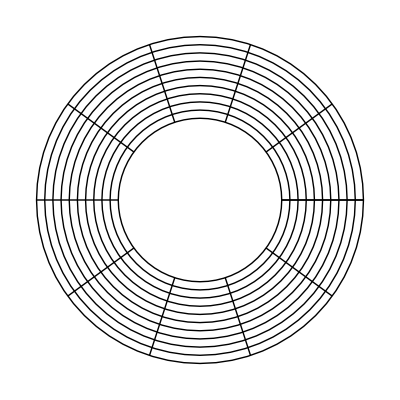
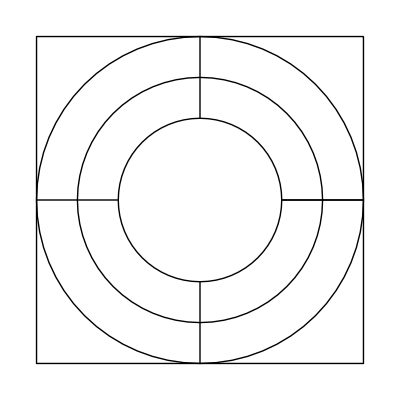

```mathematica
{ParametricPlotBezier[{s Cos[t],s Sin[t]},{s,{0.5,1}},{t,π/4 Table[i,{i,0,8}]}],
ParametricPlotBezier[{s Cos[t],s Sin[t]},{s,{0.5,1}},{t,π/4 Table[i,{i,0,8}]},Mesh->{2,4},BoundingBox->{{1,1},{-1,-1}}]}
```

```mathematica
ParametricPlot3DBezier[{Cos[t],Sin[t],t/(2π)},{t,π/4 Table[i,{i,0,16}]},LngLat->{π/7,π/7}]
ParametricPlot3DBezier[{Cos[t],Sin[t],t/(2π)},{t,π/4 Table[i,{i,0,16}]},BoundingBox->{{1,1,0},{-1,-1,2}}]
```

Limit::ztest1: 数量(1/8 - ⅈ/8)\ ⅇ^-ⅈ\ π/28 + (1/8 + ⅈ/8)\ ⅇ^ⅈ\ π/28 - ⅈ\ ⅇ^-3\ ⅈ\ π/14/4\ √2 + ⅈ\ ⅇ^3\ ⅈ\ π/14/4\ √2がゼロに等しいかどうかを判断することができませんでした．ゼロであると仮定します．

-Graphics-

-Graphics-

```mathematica
ParametricPlot3DBezier[{s Cos[t],s Sin[t],t/(2π)},{s,{0,1}},{t,π/4 Table[i,{i,0,16}]},Mesh->{5,24},LngLat->{π/7,π/7},BoundingBox->{{1,1,2},{-1,-1,0}}]
```

-Graphics-

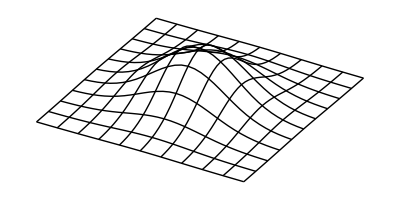

```mathematica
Plot3DBezier[Exp[-(x^2+y^2)],{x,{-2,-1,0,1,2}},{y,{-2,-1,0,1,2}}]
```

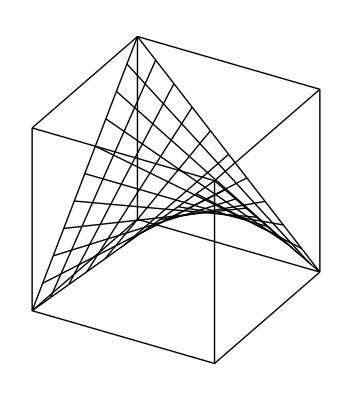
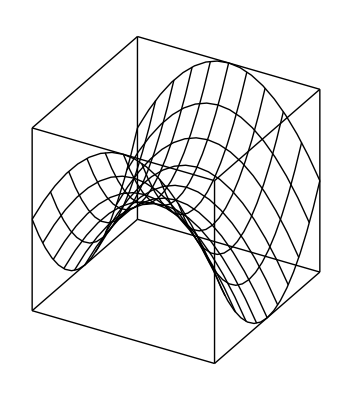

```mathematica
{Plot3DBezier[{x y},{x,{-1,0,1}},{y,{-1,0,1}},BoundingBox->{{-1,-1,-1},{1,1,1}}],
Plot3DBezier[{x^2-y^2},{x,{-1,0,1}},{y,{-1,0,1}},BoundingBox->{{-1,-1,-1},{1,1,1}}]}
```